# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 2

## 2.2 THE 1D PARTICLE IN A BOX

### 2.2.1 Basic implementation in Mathematica

```mathematica
psi1DPIB[n_,x_,L_]:=Sqrt[2/L]*Sin[n*Pi*x/L];energy1DPIB[n_,L_]:=(hbar^2*Pi^2*n^2)/(2*m*L^2);
```

```mathematica
hbar=1;(*define variables in atomic units*)
nPoints=100;(*how many points on the finite grid*)
L=5;(*length of the box in Bohr radii*)
m=1;(*set m=1 me*)
a=L/(nPoints+1); (*spacing between points*)
t=hbar^2/(2*m*a^2);(*constant for finite difference*)
```

```mathematica
V[x_]:=0;(*define the potential as zero everywhere for 1D PIB*)
```

```mathematica
(*set up the Hamiltonian matrix*)
hMatr=Table[N[
(V[i*a]+2*t)*KroneckerDelta[i,j]-t*KroneckerDelta[i,j-1]-t*KroneckerDelta[i,j+1]]
,{i,1,nPoints},{j,1,nPoints}];
```

```mathematica
Eigenvalues[hMatr] (*lots of output follows...*)
```

{815.883,815.291,814.305,812.926,811.155,808.994,806.446,803.512,800.195,796.499,792.428,787.984,783.173,777.999,772.467,766.582,760.351,753.778,746.872,739.637,732.082,724.213,716.038,707.565,698.803,689.759,680.443,670.863,661.029,650.95,640.636,630.097,619.343,608.385,597.233,585.898,574.391,562.723,550.906,538.95,526.867,514.67,502.369,489.977,477.506,464.968,452.374,439.738,427.071,414.386,401.694,389.009,376.342,363.706,351.112,338.574,326.103,313.711,301.41,289.213,277.13,265.174,253.357,241.689,230.182,218.847,207.695,196.737,185.983,175.444,165.13,155.051,145.217,135.637,126.321,117.277,108.515,100.042,91.8673,83.9984,76.4431,69.2085,62.3017,55.7294,49.4979,43.6133,38.0813,32.9072,28.096,23.6523,19.5806,15.8846,12.568,9.63406,7.08551,4.92486,3.1542,1.77524,0.789314,0.197376}

```mathematica
Eigenvalues[hMatr,-1] (*lowest one eigenvalue from finite difference*)
N[energy1DPIB[1,L]] (*compare to exact result as sanity check*)
```

{0.197376}

0.197392

### 2.2.3 How accurate is the numerical approximation?

```mathematica
Eigenvalues[hMatr,-5]
Table[N[energy1DPIB[n,L]],{n,5,1,-1}]
```

{4.92486,3.1542,1.77524,0.789314,0.197376}

{4.9348,3.15827,1.77653,0.789568,0.197392}

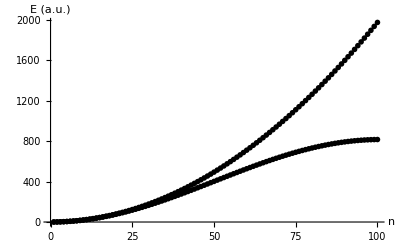

```mathematica
finiteDiffResults=Reverse[Eigenvalues[hMatr,-100]];exactResults=Table[N[energy1DPIB[n,L]],{n,1,100}];
ListPlot[{finiteDiffResults,exactResults},
AxesLabel->{"n","E (a.u.)"},Joined->True,Mesh->All]
```

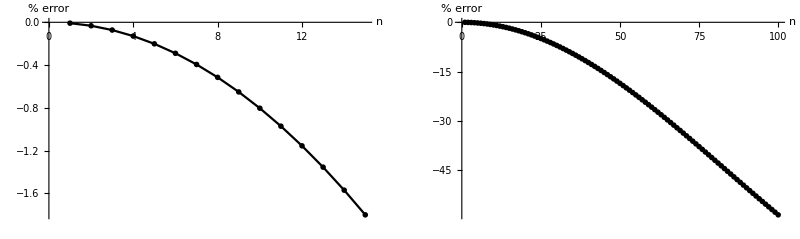

```mathematica
percentError=Table[(finiteDiffResults[[n]]-exactResults[[n]])/exactResults[[n]]*100,{n,1,100}];
GraphicsRow[
{ListPlot[percentError[[1;;15]],
AxesLabel->{"n","% error"},Joined->True,Mesh->All],
ListPlot[percentError,
AxesLabel->{"n","% error"},Joined->True,Mesh->All]}]
```

### 2.2.4 Wavefunction normalization and plotting

```mathematica
estate2=Reverse[Eigenvectors[hMatr,-2]][[2]]/Sqrt[a];Sum[estate2[[j]]^2*a,{j,1,nPoints}]
```

1.

Erratum in first printing : Missing “{“ and “}” in first line:

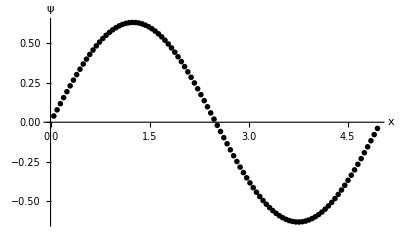

```mathematica
estate2withcoords=Table[{N[a*j],estate2[[j]]},{j,1,nPoints}];ListPlot[estate2withcoords,AxesLabel-> {"x","ψ"}]
```

### 2.2.5 Expectation values

```mathematica
xcoords=Table[ N[a*i], {i,1,nPoints}]
Sum[(Conjugate[estate2[[i]]]*xcoords[[i]]*estate2[[i]])*a, {i,1,nPoints}]
```

{0.049505,0.0990099,0.148515,0.19802,0.247525,0.29703,0.346535,0.39604,0.445545,0.49505,0.544554,0.594059,0.643564,0.693069,0.742574,0.792079,0.841584,0.891089,0.940594,0.990099,1.0396,1.08911,1.13861,1.18812,1.23762,1.28713,1.33663,1.38614,1.43564,1.48515,1.53465,1.58416,1.63366,1.68317,1.73267,1.78218,1.83168,1.88119,1.93069,1.9802,2.0297,2.07921,2.12871,2.17822,2.22772,2.27723,2.32673,2.37624,2.42574,2.47525,2.52475,2.57426,2.62376,2.67327,2.72277,2.77228,2.82178,2.87129,2.92079,2.9703,3.0198,3.06931,3.11881,3.16832,3.21782,3.26733,3.31683,3.36634,3.41584,3.46535,3.51485,3.56436,3.61386,3.66337,3.71287,3.76238,3.81188,3.86139,3.91089,3.9604,4.0099,4.05941,4.10891,4.15842,4.20792,4.25743,4.30693,4.35644,4.40594,4.45545,4.50495,4.55446,4.60396,4.65347,4.70297,4.75248,4.80198,4.85149,4.90099,4.9505}

2.5

```mathematica
Timing[
Sum[(Conjugate[estate2[[i]]]*xcoords[[i]]*estate2[[i]])*a,{i,1,nPoints}]]
```

{0.000357,2.5}

### 2.3 BEYOND THE PARTICLE IN A BOX

### 2.3.1 The finite well potential

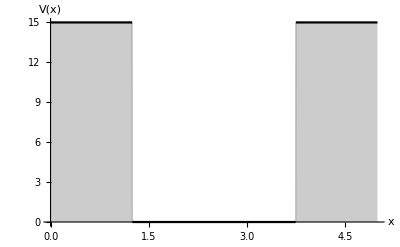

```mathematica
nPoints=100;L=5;m=1;a=L/(nPoints+1);t=1/(2*m*a^2);
Upotn=15;
V[x_]:=Piecewise[
{ {Upotn,x<L/4},
{0,L/4≤x≤3*L/4},
{Upotn,x>3*L/4} } ];
Plot[V[x],{x,0,L},Filling-> Axis,AxesLabel->{"x","V(x)"}]
```

### 2.3.3 Solution of the finite well potential

```mathematica
hMatr=Table[N[
(V[i*a]+2*t)*KroneckerDelta[i,j]-t*KroneckerDelta[i,j-1]-t*KroneckerDelta[i,j+1]],{i,1,nPoints},{j,1,nPoints}];Reverse[Eigenvalues[hMatr,-6]]
```

{0.609045,2.42118,5.38381,9.36886,13.9672,17.1852}

```mathematica
estate1=Eigenvectors[hMatr,-1][[1]]/Sqrt[a];
```

```mathematica
estate1withcoords=Table[{N[a*j],estate1[[j]]},{j,1,nPoints}];
```

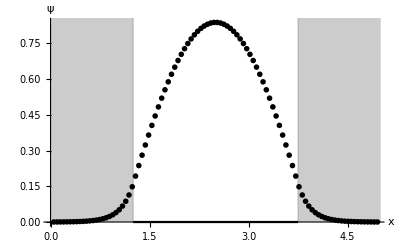

```mathematica
Show[
ListPlot[estate1withcoords,AxesLabel->{"x","ψ"}],Plot[V[x],{x,0,L},Filling->Axis]]
```

```mathematica
estate1[[1;;5]]
```

{0.000105556,0.000218558,0.000346977,0.00049987,0.000688022}

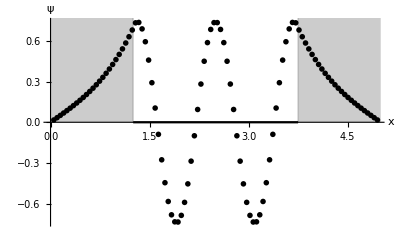

```mathematica
estate5=Reverse[Eigenvectors[hMatr,-5]][[5]]/Sqrt[a];
estate5withcoords=Table[{N[a*j],estate5[[j]]},{j,1,nPoints}];

Show[
ListPlot[estate5withcoords,AxesLabel-> {"x","ψ"}],Plot[V[x],{x,0,L},Filling-> Axis]]
```

```mathematica
estate5[[1;;5]]
```

{0.016821,0.0337271,0.050804,0.068138,0.085817}